### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9},Adjacency Matrix→{{0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,1,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{7,U1},{8,U2},{9,U3}},Switching Costs→{}|>

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

-Graphics-

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
Data/.{I1-> 2,I2->2, U1-> 1,U2->1,U3->0}
```

```mathematica
{timeheterodata,d2ehetero}=AbsolutTiming@D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}];
```

```mathematica
{timehetero,{systemhetero,resulthetero}}=AbsoluteTiming@CriticalCongestionSolver[d2ehetero]
```

It took 0.082896 to Clean the equalities and get 
NonNegative[j18-j20-jt12+jt20+jt23]&&NonNegative[jt13+jt14]&&NonNegative[j18-j20+jt20+jt23]&&NonNegative[j17+j6-jt20-jt23]&&NonNegative[3+j20-j6+jt28+jt31]&&NonNegative[j6]&&NonNegative[j10+j11+j20+j21-j24-j6]&&NonNegative[-j10+j12+j24+jt51]&&NonNegative[3-j11-j12]&&NonNegative[j10]&&NonNegative[j11]&&NonNegative[j12]&&NonNegative[2+j17-jt12]&&NonNegative[-3-j17+j18-j20+jt13+jt14+jt20+jt23]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[jt28+jt31]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[jt51]&&NonNegative[j24]&&NonNegative[2+j17-jt12]&&NonNegative[-3-j17+j18-j20+jt13+jt14+jt20+jt23]&&NonNegative[3+j17-jt12-jt13-jt14]&&NonNegative[-2-j17+jt12+jt13+jt14]&&NonNegative[j18-j20-jt12+jt20+jt23]&&NonNegative[j17]&&NonNegative[2-jt12]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[-3+j18-j20+j6+jt14-jt28-jt31]&&NonNegative[3+j20-j6-jt14+jt28+jt31]&&NonNegative[-j17-j6+jt13+jt20+jt23+jt28+jt31]&&NonNegative[j17+j6-jt13-jt20-jt23]&&NonNegative[j18-j20+jt23]&&NonNegative[jt20]&&NonNegative[j17-jt23]&&NonNegative[j6-jt20]&&NonNegative[jt23]&&NonNegative[j20-jt23]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[3+j20-j6-jt25-jt26+jt28+jt31]&&NonNegative[jt28]&&NonNegative[-j10+j12+j24-jt26+jt51]&&NonNegative[j10-j12+j21-j24+jt26-jt28-jt51]&&NonNegative[jt31]&&NonNegative[j10+j11+j20+j21-j24-j6-jt25]&&NonNegative[-j10-j11-j20-j21+j24+j6+jt25-jt31+jt51]&&NonNegative[j21-jt44]&&NonNegative[jt38]&&NonNegative[-j21+j6-jt38+jt44]&&NonNegative[j20-jt43]&&NonNegative[j10-jt38]&&NonNegative[j11+j21-j24-j6+jt38+jt43]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[j24-jt43-jt44]&&NonNegative[j24]&&NonNegative[-j10+j12+jt51]&&NonNegative[jt51]&&NonNegative[j10-jt51]&&(2+j17-jt12==0||j18-j20-jt12+jt20+jt23==0)&&(-3-j17+j18-j20+jt13+jt14+jt20+jt23==0||jt13+jt14==0)&&(j17==0||j18-j20+jt20+jt23==0)&&(j18==0||j17+j6-jt20-jt23==0)&&(jt28+jt31==0||3+j20-j6+jt28+jt31==0)&&(j20==0||j6==0)&&(j21==0||j10+j11+j20+j21-j24-j6==0)&&(jt51==0||-j10+j12+j24+jt51==0)&&(j24==0||j10==0)&&(2+j17-jt12==0||-3-j17+j18-j20+jt13+jt14+jt20+jt23==0)&&(jt13==0||-3+j18-j20+j6+jt14-jt28-jt31==0)&&(jt14==0||-j17-j6+jt13+jt20+jt23+jt28+jt31==0)&&(3+j20-j6-jt14+jt28+jt31==0||j17+j6-jt13-jt20-jt23==0)&&(j18-j20+jt23==0||j17-jt23==0)&&(jt20==0||jt23==0)&&(j6-jt20==0||j20-jt23==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(-j10+j12+j24-jt26+jt51==0||j10+j11+j20+j21-j24-j6-jt25==0)&&(j21-jt44==0||j20-jt43==0)&&(jt38==0||jt43==0)&&(j10-jt38==0||jt44==0)&&(j24==0||jt51==0)&&(j18-j20-jt12+jt20+jt23==0||j17==0)&&(2+j17-jt12==0||3+j17-j18+j20-jt20-jt23-u1+u16==0)&&(-3-j17+j18-j20+jt13+jt14+jt20+jt23==0||-3-j17+j18-j20+jt20+jt23+u1-u16==0)&&(3+j17-jt12-jt13-jt14==0||u1-u13==0)&&(-2-j17+jt12+jt13+jt14==0||3+j17-j18+j20-jt20-jt23-u13+u16==0)&&(j18-j20-jt12+jt20+jt23==0||-2-2 j17+2 j18-2 j20+2 jt20+2 jt23-u1+u17==0)&&(j17==0||2+2 j17-2 j18+2 j20-2 jt20-2 jt23+u1-u17==0)&&(2-jt12==0||2+j17-j18+j20-jt20-jt23+u1-u14==0)&&(jt12==0||-j17+j18-j20+jt20+jt23-u14+u17==0)&&(jt13==0||j17-j18+j6-jt20-jt23-u16+u18==0)&&(jt14==0||3+j20-j6-u16+u19==0)&&(-3+j18-j20+j6+jt14-jt28-jt31==0||-j17+j18-j6+jt20+jt23+u16-u18==0)&&(3+j20-j6-jt14+jt28+jt31==0||3-j17+j18+j20-2 j6+jt20+jt23-u18+u19==0)&&(-j17-j6+jt13+jt20+jt23+jt28+jt31==0||-3-j20+j6+u16-u19==0)&&(j17+j6-jt13-jt20-jt23==0||-3+j17-j18-j20+2 j6-jt20-jt23+u18-u19==0)&&(j18-j20+jt23==0||-u17+u18==0)&&(jt20==0||-j20+j6-u17+u20==0)&&(j17-jt23==0||u17-u18==0)&&(j6-jt20==0||-j20+j6-u18+u20==0)&&(jt23==0||j20-j6+u17-u20==0)&&(j20-jt23==0||j20-j6+u18-u20==0)&&(jt25==0||j10+j11+j20-j24-j6-u19+u21==0)&&(jt26==0||-j10+j12+j24-u19+u22==0)&&(3+j20-j6-jt25-jt26+jt28+jt31==0||1-u19==0)&&(jt28==0||-j10-j11-j20+j24+j6+u19-u21==0)&&(-j10+j12+j24-jt26+jt51==0||-2 j10-j11+j12-j20+2 j24+j6-u21+u22==0)&&(j10-j12+j21-j24+jt26-jt28-jt51==0||1-j10-j11-j20+j24+j6-u21==0)&&(jt31==0||j10-j12-j24+u19-u22==0)&&(j10+j11+j20+j21-j24-j6-jt25==0||2 j10+j11-j12+j20-2 j24-j6+u21-u22==0)&&(-j10-j11-j20-j21+j24+j6+jt25-jt31+jt51==0||1+j10-j12-j24-u22==0)&&(j21-jt44==0||-u20+u21==0)&&(jt38==0||u10-u20==0)&&(-j21+j6-jt38+jt44==0||2-u20==0)&&(j20-jt43==0||u20-u21==0)&&(j10-jt38==0||u10-u21==0)&&(j11+j21-j24-j6+jt38+jt43==0||2-u21==0)&&(jt43==0||-u10+u20==0)&&(jt44==0||-u10+u21==0)&&(j24-jt43-jt44==0||2-u10==0)&&(j24==0||-j10+j24+u10-u22==0)&&(-j10+j12+jt51==0||3-u22==0)&&(jt51==0||j10-j24-u10+u22==0)&&(j10-jt51==0||3+j10-j24-u10==0)

$Aborted

```mathematica
Keys@d2ehetero
```

{Data,BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,SwitchingCosts,OutRules,InRules,EntryArgs,EntryDataAssociation,jays,NonZeroEntryCurrents,ExitCosts,EqCurrentCompCon,EqTransitionCompCon,EqCompCon,EqAllComp,EqPosCon,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EqEntryIn,EqExitValues,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,EqAllAll,BoundaryRules,RulesEntryIn,RulesExitValues,Nlhs,MinimalTimeRhs,EqCriticalCase,Nrhs,EqGeneralCase}

```mathematica
d2e["EqCurrentCompCon"]
d2e["EqSwitchingConditions"]
```

(j15==0||j1==0)&&(j16==0||j2==0)&&(j17==0||j3==0)&&(j18==0||j4==0)&&(j19==0||j5==0)&&(j20==0||j6==0)&&(j21==0||j7==0)&&(j22==0||j8==0)&&(j23==0||j9==0)&&(j24==0||j10==0)&&(j25==0||j11==0)&&(j26==0||j12==0)&&(j27==0||j13==0)&&(j28==0||j14==0)

u2≥u27&&u1==u2&&u28≤u3&&u15==u3&&u4==u5&&u16==u5&&u18==u6&&u17==u6&&u8≤u9&&u7==u8&&u19==u7&&u11≥u21&&u20==u21&&u10==u21&&u12≥u24&&u22==u24

```mathematica
d2ehetero["EqAll"]
```

NonNegative[j1]&&NonNegative[j2]&&NonNegative[j3]&&NonNegative[j4]&&NonNegative[j5]&&NonNegative[j6]&&NonNegative[j7]&&NonNegative[j8]&&NonNegative[j9]&&NonNegative[j10]&&NonNegative[j11]&&NonNegative[j12]&&NonNegative[j13]&&NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[j19]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[j22]&&NonNegative[j23]&&NonNegative[j24]&&NonNegative[j25]&&NonNegative[j26]&&NonNegative[j27]&&NonNegative[j28]&&NonNegative[jt1]&&NonNegative[jt2]&&NonNegative[jt3]&&NonNegative[jt4]&&NonNegative[jt5]&&NonNegative[jt6]&&NonNegative[jt7]&&NonNegative[jt8]&&NonNegative[jt9]&&NonNegative[jt10]&&NonNegative[jt11]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[jt15]&&NonNegative[jt16]&&NonNegative[jt17]&&NonNegative[jt18]&&NonNegative[jt19]&&NonNegative[jt20]&&NonNegative[jt21]&&NonNegative[jt22]&&NonNegative[jt23]&&NonNegative[jt24]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[jt27]&&NonNegative[jt28]&&NonNegative[jt29]&&NonNegative[jt30]&&NonNegative[jt31]&&NonNegative[jt32]&&NonNegative[jt33]&&NonNegative[jt34]&&NonNegative[jt35]&&NonNegative[jt36]&&NonNegative[jt37]&&NonNegative[jt38]&&NonNegative[jt39]&&NonNegative[jt40]&&NonNegative[jt41]&&NonNegative[jt42]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[jt45]&&NonNegative[jt46]&&NonNegative[jt47]&&NonNegative[jt48]&&NonNegative[jt49]&&NonNegative[jt50]&&NonNegative[jt51]&&NonNegative[jt52]&&NonNegative[jt53]&&NonNegative[jt54]&&j15==jt1+jt2&&j16==jt3+jt4&&j13==jt5+jt6&&j1==jt7+jt8&&j17==jt10+jt9&&j14==jt11+jt12&&j2==jt13+jt14&&j18==jt15+jt16&&j19==jt17+jt18&&j3==jt19+jt20&&j4==jt21+jt22&&j20==jt23+jt24&&j5==jt25+jt26+jt27&&j21==jt28+jt29+jt30&&j22==jt31+jt32+jt33&&j23==jt34+jt35+jt36&&j6==jt37+jt38+jt39&&j7==jt40+jt41+jt42&&j24==jt43+jt44+jt45&&j25==jt46+jt47+jt48&&j8==jt49+jt50&&j10==jt51+jt52&&j26==jt53+jt54&&j1==jt3+jt5&&j2==jt1+jt6&&j27==jt2+jt4&&j15==jt11+jt9&&j3==jt12+jt7&&j28==jt10+jt8&&j16==jt15+jt17&&j4==jt13+jt18&&j5==jt14+jt16&&j17==jt21+jt23&&j18==jt19+jt24&&j6==jt20+jt22&&j19==jt28+jt31+jt34&&j7==jt25+jt32+jt35&&j8==jt26+jt29+jt36&&j9==jt27+jt30+jt33&&j20==jt40+jt43+jt46&&j21==jt37+jt44+jt47&&j10==jt38+jt41+jt48&&j11==jt39+jt42+jt45&&j22==jt51+jt53&&j24==jt49+jt54&&j12==jt50+jt52&&j13==1&&j14==2&&u23==1&&u25==2&&u26==3&&u2≥u27&&u1==u2&&u28≤u3&&u15==u3&&u4==u5&&u16==u5&&u18==u6&&u17==u6&&u8≤u9&&u7==u8&&u19==u7&&u11≥u21&&u20==u21&&u10==u21&&u12≥u24&&u22==u24&&-u13+u27==0&&-u14+u28==0&&u23-u9==0&&-u11+u25==0&&-u12+u26==0

It took 0.089199 to Clean the equalities and get 
NonNegative[23/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[jt13+jt14]&&NonNegative[23/15+j10/15+j11/15+j17-j24/15]&&NonNegative[17/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23]&&NonNegative[28/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31]&&NonNegative[17/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15]&&NonNegative[-17/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15]&&NonNegative[-17/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51]&&NonNegative[62/15-(41 j10)/15-(26 j11)/15+(41 j24)/15]&&NonNegative[j10]&&NonNegative[j11]&&NonNegative[-17/15+(41 j10)/15+(11 j11)/15-(41 j24)/15]&&NonNegative[2+j17-jt12]&&NonNegative[-22/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[j17]&&NonNegative[23/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23]&&NonNegative[jt28+jt31]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[jt51]&&NonNegative[j24]&&NonNegative[2+j17-jt12]&&NonNegative[-22/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[3+j17-jt12-jt13-jt14]&&NonNegative[-2-j17+jt12+jt13+jt14]&&NonNegative[23/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[j17]&&NonNegative[2-jt12]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[-1/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31]&&NonNegative[28/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31]&&NonNegative[-17/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31]&&NonNegative[17/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23]&&NonNegative[23/15+j10/15+j11/15+j17-j24/15-jt20]&&NonNegative[jt20]&&NonNegative[j17-jt23]&&NonNegative[17/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20]&&NonNegative[jt23]&&NonNegative[j20-jt23]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[28/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31]&&NonNegative[jt28]&&NonNegative[-17/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51]&&NonNegative[17/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51]&&NonNegative[jt31]&&NonNegative[-17/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25]&&NonNegative[17/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51]&&NonNegative[j21-jt44]&&NonNegative[jt38]&&NonNegative[17/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44]&&NonNegative[j20-jt43]&&NonNegative[j10-jt38]&&NonNegative[-17/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[j24-jt43-jt44]&&NonNegative[j24]&&NonNegative[-17/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51]&&NonNegative[jt51]&&NonNegative[j10-jt51]&&11/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10≥u13&&u14≤8/3+j10/3+j11/3-j24/3+u10&&-17/15+(11 j10)/15+(11 j11)/15-(11 j24)/15+u10≤1&&2≥u10&&3≥-j10+j24+u10&&(2+j17-jt12==0||23/15+j10/15+j11/15+j17-j24/15-jt12==0)&&(-22/15+j10/15+j11/15-j24/15+jt13+jt14==0||jt13+jt14==0)&&(j17==0||23/15+j10/15+j11/15+j17-j24/15==0)&&(23/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23==0||17/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23==0)&&(jt28+jt31==0||28/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31==0)&&(j20==0||17/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15==0)&&(j21==0||-17/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15==0)&&(jt51==0||-17/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51==0)&&(j24==0||j10==0)&&(2+j17-jt12==0||-22/15+j10/15+j11/15-j24/15+jt13+jt14==0)&&(jt13==0||-1/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31==0)&&(jt14==0||-17/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31==0)&&(28/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31==0||17/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23==0)&&(23/15+j10/15+j11/15+j17-j24/15-jt20==0||j17-jt23==0)&&(jt20==0||jt23==0)&&(17/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20==0||j20-jt23==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(-17/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51==0||-17/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25==0)&&(j21-jt44==0||j20-jt43==0)&&(jt38==0||jt43==0)&&(j10-jt38==0||jt44==0)&&(j24==0||jt51==0)&&(23/15+j10/15+j11/15+j17-j24/15-jt12==0||j17==0)&&(3+j17-jt12-jt13-jt14==0||11/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(-2-j17+jt12+jt13+jt14==0||11/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(2-jt12==0||8/3+j10/3+j11/3-j24/3+u10-u14==0)&&(jt12==0||8/3+j10/3+j11/3-j24/3+u10-u14==0)&&(28/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31==0||32/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(17/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51==0||32/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(17/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51==0||32/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(17/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44==0||2-u10==0)&&(-17/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43==0||2-u10==0)&&(j24-jt43-jt44==0||2-u10==0)&&(-17/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51==0||3+j10-j24-u10==0)&&(j10-jt51==0||3+j10-j24-u10==0)

NewReduce: ZAnd took 209.91 to get to 
(41 j10==17&&j11==0&&j17==0&&j20==0&&41 j21==34&&j24==0&&41 jt12==64&&jt13==0&&41 jt14==59&&41 jt20==51&&jt23==0&&jt25==0&&jt26==0&&jt28+jt31==0&&41 jt38==17&&jt43==0&&jt44==0&&41 jt51==17&&41 u10==75&&41 u13==172&&41 u14==190&&NonNegative[510/41-15 jt28]&&NonNegative[-jt28]&&NonNegative[jt28]&&NonNegative[255/41+15 jt28])||(41 j10==17&&j11==0&&j17==0&&j20==0&&41 j21==34&&j24==0&&41 jt12==64&&jt13==0&&41 jt14==59&&41 jt20==51&&jt23==0&&jt25==0&&jt28==0&&jt31==0&&41 jt38==17&&jt43==0&&jt44==0&&41 jt51==17&&41 u10==75&&41 u13==172&&41 u14==190&&NonNegative[1080/41-15 jt26]&&NonNegative[-jt26]&&NonNegative[jt26]&&NonNegative[510/41+15 jt26])||(41 j10==17&&j11==0&&j17==0&&j20==0&&41 j21==34&&j24==0&&41 jt12==64&&jt13==0&&41 jt14==59&&41 jt20==51&&jt23==0&&jt26==0&&jt28==0&&jt31==0&&41 jt38==17&&jt43==0&&jt44==0&&41 jt51==17&&41 u10==75&&41 u13==172&&41 u14==190&&NonNegative[1080/41-15 jt25]&&NonNegative[-jt25]&&NonNegative[jt25]&&NonNegative[255/41+15 jt25])

NewReduce: Reduce took 0.005548 to get to 
jt31==0&&jt28==0&&jt26==0&&jt25==0&&u14==190/41&&u13==172/41&&u10==75/41&&jt51==17/41&&jt44==0&&jt43==0&&jt38==17/41&&jt23==0&&jt20==51/41&&jt14==59/41&&jt13==0&&jt12==64/41&&j24==0&&j21==34/41&&j20==0&&j17==0&&j11==0&&j10==17/41

It took 209.924 to NewReduce to jt31==0&&jt28==0&&jt26==0&&jt25==0&&41 u14==190&&41 u13==172&&41 u10==75&&41 jt51==17&&jt44==0&&jt43==0&&41 jt38==17&&jt23==0&&41 jt20==51&&41 jt14==59&&jt13==0&&41 jt12==64&&j24==0&&41 j21==34&&j20==0&&j17==0&&j11==0&&41 j10==17

DataToEquations: Critical congestion solved.

{210.031,{True,<|j1→0,j12→0,j13→1,j14→2,j15→18/41,j16→0,j18→13/41,j19→0,j2→59/41,j22→17/41,j23→0,j25→0,j26→0,j27→0,j28→0,j3→64/41,j4→0,j5→72/41,j6→51/41,j7→0,j8→0,j9→3,jt1→18/41,jt10→0,jt11→18/41,jt15→0,jt16→13/41,jt17→0,jt18→0,jt19→13/41,jt2→0,jt21→0,jt22→0,jt24→0,jt27→72/41,jt29→0,jt3→0,jt30→34/41,jt32→0,jt33→17/41,jt34→0,jt35→0,jt36→0,jt37→34/41,jt39→0,jt4→0,jt40→0,jt41→0,jt42→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→0,jt52→0,jt53→0,jt54→0,jt6→1,jt7→0,jt8→0,jt9→0,u1→172/41,u11→2,u12→3,u15→190/41,u16→113/41,u17→126/41,u18→126/41,u19→1,u2→172/41,u20→75/41,u21→75/41,u22→58/41,u23→1,u24→58/41,u25→2,u26→3,u27→172/41,u28→190/41,u3→190/41,u4→113/41,u5→113/41,u6→126/41,u7→1,u8→1,u9→1,j10→17/41,j11→0,j17→0,j20→0,j21→34/41,j24→0,jt12→64/41,jt13→0,jt14→59/41,jt20→51/41,jt23→0,jt25→0,jt26→0,jt28→0,jt31→0,jt38→17/41,jt43→0,jt44→0,jt51→17/41,u10→75/41,u13→172/41,u14→190/41|>}}

```mathematica
d2e1=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
```

```mathematica
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming
```

It took 0.101043to Clean the equalities and get 
NonNegative[64/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[jt13+jt14]&&NonNegative[64/15+j10/15+j11/15+j17-j24/15]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23]&&NonNegative[74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15]&&NonNegative[-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15]&&NonNegative[-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51]&&NonNegative[166/15-(41 j10)/15-(26 j11)/15+(41 j24)/15]&&NonNegative[j10]&&NonNegative[j11]&&NonNegative[-46/15+(41 j10)/15+(11 j11)/15-(41 j24)/15]&&NonNegative[6+j17-jt12]&&NonNegative[-56/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[j17]&&NonNegative[64/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23]&&NonNegative[jt28+jt31]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[jt51]&&NonNegative[j24]&&NonNegative[6+j17-jt12]&&NonNegative[-56/15+j10/15+j11/15-j24/15+jt13+jt14]&&NonNegative[8+j17-jt12-jt13-jt14]&&NonNegative[-6-j17+jt12+jt13+jt14]&&NonNegative[64/15+j10/15+j11/15+j17-j24/15-jt12]&&NonNegative[j17]&&NonNegative[6-jt12]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[-2/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31]&&NonNegative[74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31]&&NonNegative[-46/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23]&&NonNegative[64/15+j10/15+j11/15+j17-j24/15-jt20]&&NonNegative[jt20]&&NonNegative[j17-jt23]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20]&&NonNegative[jt23]&&NonNegative[j20-jt23]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31]&&NonNegative[jt28]&&NonNegative[-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51]&&NonNegative[46/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51]&&NonNegative[jt31]&&NonNegative[-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25]&&NonNegative[46/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51]&&NonNegative[j21-jt44]&&NonNegative[jt38]&&NonNegative[46/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44]&&NonNegative[j20-jt43]&&NonNegative[j10-jt38]&&NonNegative[-46/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43]&&NonNegative[jt43]&&NonNegative[jt44]&&NonNegative[j24-jt43-jt44]&&NonNegative[j24]&&NonNegative[-46/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51]&&NonNegative[jt51]&&NonNegative[j10-jt51]&&28/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10≥u13&&u14≤22/3+j10/3+j11/3-j24/3+u10&&-46/15+(11 j10)/15+(11 j11)/15-(11 j24)/15+u10≤1&&2≥u10&&0≥-j10+j24+u10&&(6+j17-jt12==0||64/15+j10/15+j11/15+j17-j24/15-jt12==0)&&(-56/15+j10/15+j11/15-j24/15+jt13+jt14==0||jt13+jt14==0)&&(j17==0||64/15+j10/15+j11/15+j17-j24/15==0)&&(64/15+j10/15+j11/15+j17+j20-j24/15-jt20-jt23==0||46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt20-jt23==0)&&(jt28+jt31==0||74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15+jt28+jt31==0)&&(j20==0||46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15==0)&&(j21==0||-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15==0)&&(jt51==0||-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15+jt51==0)&&(j24==0||j10==0)&&(6+j17-jt12==0||-56/15+j10/15+j11/15-j24/15+jt13+jt14==0)&&(jt13==0||-2/3+j10/3+j11/3+j17+j20-j24/3+jt14-jt20-jt23-jt28-jt31==0)&&(jt14==0||-46/15-(4 j10)/15-(4 j11)/15-j17-j20+(4 j24)/15+jt13+jt20+jt23+jt28+jt31==0)&&(74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt14+jt28+jt31==0||46/15+(4 j10)/15+(4 j11)/15+j17+j20-(4 j24)/15-jt13-jt20-jt23==0)&&(64/15+j10/15+j11/15+j17-j24/15-jt20==0||j17-jt23==0)&&(jt20==0||jt23==0)&&(46/15+(4 j10)/15+(4 j11)/15+j20-(4 j24)/15-jt20==0||j20-jt23==0)&&(jt25==0||jt28==0)&&(jt26==0||jt31==0)&&(-46/15+(26 j10)/15+(11 j11)/15-(26 j24)/15-jt26+jt51==0||-46/15+(11 j10)/15+(11 j11)/15+j21-(11 j24)/15-jt25==0)&&(j21-jt44==0||j20-jt43==0)&&(jt38==0||jt43==0)&&(j10-jt38==0||jt44==0)&&(j24==0||jt51==0)&&(64/15+j10/15+j11/15+j17-j24/15-jt12==0||j17==0)&&(8+j17-jt12-jt13-jt14==0||28/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(-6-j17+jt12+jt13+jt14==0||28/5+(2 j10)/5+(2 j11)/5-(2 j24)/5+u10-u13==0)&&(6-jt12==0||22/3+j10/3+j11/3-j24/3+u10-u14==0)&&(jt12==0||22/3+j10/3+j11/3-j24/3+u10-u14==0)&&(74/15-(4 j10)/15-(4 j11)/15+(4 j24)/15-jt25-jt26+jt28+jt31==0||61/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(46/15-(26 j10)/15-(11 j11)/15+j21+(26 j24)/15+jt26-jt28-jt51==0||61/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(46/15-(11 j10)/15-(11 j11)/15-j21+(11 j24)/15+jt25-jt31+jt51==0||61/15-(11 j10)/15-(11 j11)/15+(11 j24)/15-u10==0)&&(46/15+(4 j10)/15+(4 j11)/15+j20-j21-(4 j24)/15-jt38+jt44==0||2-u10==0)&&(-46/15-(4 j10)/15+(11 j11)/15-j20+j21-(11 j24)/15+jt38+jt43==0||2-u10==0)&&(j24-jt43-jt44==0||2-u10==0)&&(-46/15+(26 j10)/15+(11 j11)/15-(41 j24)/15+jt51==0||j10-j24-u10==0)&&(j10-jt51==0||j10-j24-u10==0)

It took 256.567to NewReduce to 0≤jt26≤1&&jt44==0&&jt38==2&&jt31==0&&jt28==0&&jt25==0&&11 u14==113&&11 u13==96&&u10==2&&jt51==0&&jt43==0&&jt23==0&&11 jt20==42&&11 jt14==39&&jt13==0&&11 jt12==49&&j24==0&&j21==1&&j20==0&&j17==0&&11 j11==9&&j10==2

DataToEquations: The system does not have the original structure: 0≤jt26≤1&&jt44==0&&jt38==2&&jt31==0&&jt28==0&&jt25==0&&11 u14==113&&11 u13==96&&u10==2&&jt51==0&&jt43==0&&jt23==0&&11 jt20==42&&11 jt14==39&&jt13==0&&11 jt12==49&&j24==0&&j21==1&&j20==0&&j17==0&&11 j11==9&&j10==2

DataToEquations: Multiple solutions 
		0≤jt26≤1

DataToEquations: There are multiple solutions for the given data.

{256.688,{0≤jt26≤1,<|j1→0,j12→3,j13→2,j14→6,j15→17/11,j16→0,j18→7/11,j19→0,j2→39/11,j22→0,j23→0,j25→0,j26→0,j27→0,j28→0,j3→49/11,j4→0,j5→46/11,j6→42/11,j7→0,j8→1,j9→46/11,jt1→17/11,jt10→0,jt11→17/11,jt15→0,jt16→7/11,jt17→0,jt18→0,jt19→7/11,jt2→0,jt21→0,jt22→0,jt24→0,jt27→46/11-jt26,jt29→1-jt26,jt3→0,jt30→jt26,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→1,jt39→9/11,jt4→0,jt40→0,jt41→0,jt42→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→1,jt52→2,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→96/11,u11→2,u12→0,u15→113/11,u16→57/11,u17→64/11,u18→64/11,u19→1,u2→96/11,u20→2,u21→2,u22→0,u23→1,u24→0,u25→2,u26→0,u27→96/11,u28→113/11,u3→113/11,u4→57/11,u5→57/11,u6→64/11,u7→1,u8→1,u9→1,j10→2,j11→9/11,j17→0,j20→0,j21→1,j24→0,jt12→49/11,jt13→0,jt14→39/11,jt20→42/11,jt23→0,jt25→0,jt28→0,jt31→0,jt38→2,jt43→0,jt44→0,jt51→0,u10→2,u13→96/11,u14→113/11|>}}

```mathematica
jt1105->46/11-jt1104,jt1107->1-jt1104,jt1108->jt1104
```

```mathematica
d2e["jvars"]/.rules
```

<|{2,1->2}→0,{3,1->3}→39/11,{4,2->4}→49/11,{4,3->4}→0,{5,3->5}→46/11,{6,4->6}→42/11,{6,5->6}→0,{7,5->7}→1,{ex1048,5->ex1048}→46/11,{7,6->7}→2,{ex1049,6->ex1049}→9/11,{ex1050,7->ex1050}→3,{1,en1046->1}→2,{2,en1047->2}→6,{1,1->2}→17/11,{1,1->3}→0,{2,2->4}→0,{3,3->4}→7/11,{3,3->5}→0,{4,4->6}→0,{5,5->6}→1,{5,5->7}→0,{5,5->ex1048}→0,{6,6->7}→0,{6,6->ex1049}→0,{7,7->ex1050}→0,{en1046,en1046->1}→0,{en1047,en1047->2}→0|>

```mathematica
d2e["jtvars"]//Length
```

54

```mathematica
d2e["jvars"]//Length
```

28

```mathematica
d2e["jtvars"]/.rules
```

<|{1,1->2,1->3}→17/11,{1,1->2,en1046->1}→0,{1,1->3,1->2}→0,{1,1->3,en1046->1}→0,{1,en1046->1,1->2}→0,{1,en1046->1,1->3}→2,{2,1->2,2->4}→0,{2,1->2,en1047->2}→0,{2,2->4,1->2}→0,{2,2->4,en1047->2}→0,{2,en1047->2,1->2}→17/11,{2,en1047->2,2->4}→49/11,{3,1->3,3->4}→0,{3,1->3,3->5}→39/11,{3,3->4,1->3}→0,{3,3->4,3->5}→7/11,{3,3->5,1->3}→0,{3,3->5,3->4}→0,{4,2->4,3->4}→7/11,{4,2->4,4->6}→42/11,{4,3->4,2->4}→0,{4,3->4,4->6}→0,{4,4->6,2->4}→0,{4,4->6,3->4}→0,{5,3->5,5->6}→0,{5,3->5,5->7}→jt1104,{5,3->5,5->ex1048}→46/11-jt1104,{5,5->6,3->5}→0,{5,5->6,5->7}→1-jt1104,{5,5->6,5->ex1048}→jt1104,{5,5->7,3->5}→0,{5,5->7,5->6}→0,{5,5->7,5->ex1048}→0,{5,5->ex1048,3->5}→0,{5,5->ex1048,5->6}→0,{5,5->ex1048,5->7}→0,{6,4->6,5->6}→1,{6,4->6,6->7}→2,{6,4->6,6->ex1049}→9/11,{6,5->6,4->6}→0,{6,5->6,6->7}→0,{6,5->6,6->ex1049}→0,{6,6->7,4->6}→0,{6,6->7,5->6}→0,{6,6->7,6->ex1049}→0,{6,6->ex1049,4->6}→0,{6,6->ex1049,5->6}→0,{6,6->ex1049,6->7}→0,{7,5->7,6->7}→0,{7,5->7,7->ex1050}→1,{7,6->7,5->7}→0,{7,6->7,7->ex1050}→2,{7,7->ex1050,5->7}→0,{7,7->ex1050,6->7}→0|>

```mathematica
d2e["EqExitValues"]
```

```mathematica
d2e["ExitCosts"]
```

<|ex1048→1,ex1049→2,ex1050→0|>

```mathematica
Gra
```

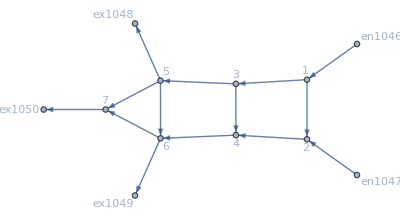

```mathematica
Graph[d2e["FG"],GraphLayout->"SpringElectricalEmbedding"]
```

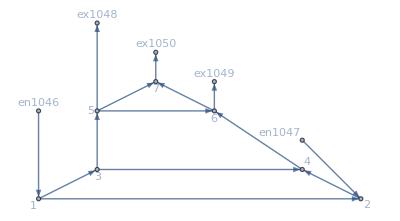

```mathematica
Table[Graph[d2e["FG"],GraphLayout->l],{l,{}}]
```

```mathematica
Keys@d2e
d2e["EqBalanceSplittingCurrents"]&&d2e["EqBalanceGatheringCurrents"]/.MapThread[Rule,{d2e["js"], (d2e["js"]/.rules)}]
```

{Data,BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,SwitchingCosts,OutRules,InRules,EntryArgs,EntryDataAssociation,jays,NonZeroEntryCurrents,ExitCosts,EqCurrentCompCon,EqTransitionCompCon,EqCompCon,EqAllComp,EqPosCon,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EqEntryIn,EqExitValues,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,EqAllAll,BoundaryRules,RulesEntryIn,RulesExitValues,Nlhs,MinimalTimeRhs,EqCriticalCase,Nrhs,EqGeneralCase}

17/11==jt1079+jt1080&&0==jt1081+jt1082&&2==jt1083+jt1084&&0==jt1085+jt1086&&0==jt1087+jt1088&&6==jt1089+jt1090&&39/11==jt1091+jt1092&&7/11==jt1093+jt1094&&0==jt1095+jt1096&&49/11==jt1097+jt1098&&0==jt1099+jt1100&&0==jt1101+jt1102&&46/11==jt1103+jt1104+jt1105&&1==jt1106+jt1107+jt1108&&0==jt1109+jt1110+jt1111&&0==jt1112+jt1113+jt1114&&42/11==jt1115+jt1116+jt1117&&0==jt1118+jt1119+jt1120&&0==jt1121+jt1122+jt1123&&0==jt1124+jt1125+jt1126&&1==jt1127+jt1128&&2==jt1129+jt1130&&0==jt1131+jt1132&&0==jt1081+jt1083&&39/11==jt1079+jt1084&&0==jt1080+jt1082&&17/11==jt1087+jt1089&&49/11==jt1085+jt1090&&0==jt1086+jt1088&&0==jt1093+jt1095&&0==jt1091+jt1096&&46/11==jt1092+jt1094&&0==jt1099+jt1101&&7/11==jt1097+jt1102&&42/11==jt1098+jt1100&&0==jt1106+jt1109+jt1112&&0==jt1103+jt1110+jt1113&&1==jt1104+jt1107+jt1114&&46/11==jt1105+jt1108+jt1111&&0==jt1118+jt1121+jt1124&&1==jt1115+jt1122+jt1125&&2==jt1116+jt1119+jt1126&&9/11==jt1117+jt1120+jt1123&&0==jt1129+jt1131&&0==jt1127+jt1132&&3==jt1128+jt1130

```mathematica
d2e1=D2E[Data/.{I1-> 2,I2->6, U1-> 0,U2->0,U3->0}];
{time1,{system1,rules1}}=CriticalCongestionSolver[d2e1]//AbsoluteTiming
```

It took 0.15278 to Clean the equalities and get 
NonNegative[186/41+j10/41-j12/41+j19+j28/41-jt12-jt51/41]&&NonNegative[jt13+jt14]&&NonNegative[186/41+j10/41-j12/41+j19+j28/41-jt51/41]&&NonNegative[170/41+(4 j10)/41-(4 j12)/41+j19+j22+(4 j28)/41-jt20-jt23-(4 jt51)/41]&&NonNegative[jt25+jt26]&&NonNegative[170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-(4 jt51)/41]&&NonNegative[166/41+(15 j10)/41-(15 j12)/41+j22+(15 j28)/41-jt32-jt35+jt45-(15 jt51)/41]&&NonNegative[162/41-(15 j10)/41+(15 j12)/41-(15 j28)/41+jt39+(15 jt51)/41]&&NonNegative[166/41+(15 j10)/41-(15 j12)/41+(15 j28)/41+jt45-(15 jt51)/41]&&NonNegative[j10]&&NonNegative[162/41-(56 j10)/41+(15 j12)/41-(15 j28)/41+(56 jt51)/41]&&NonNegative[j12]&&NonNegative[166/41+(15 j10)/41-(56 j12)/41+(56 j28)/41-(15 jt51)/41]&&NonNegative[j10+j12-j28-jt51]&&NonNegative[6+j19-jt12]&&NonNegative[-142/41+j10/41-j12/41+j28/41+jt13+jt14-jt51/41]&&NonNegative[j19]&&NonNegative[186/41+j10/41-j12/41+j19+j22+j28/41-jt20-jt23-jt51/41]&&NonNegative[-158/41+(4 j10)/41-(4 j12)/41+(4 j28)/41+jt25+jt26-(4 jt51)/41]&&NonNegative[j22]&&NonNegative[170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-jt32-jt35+jt45-(4 jt51)/41]&&NonNegative[jt39]&&NonNegative[jt45]&&NonNegative[jt51]&&NonNegative[j28]&&NonNegative[6+j19-jt12]&&NonNegative[-142/41+j10/41-j12/41+j28/41+jt13+jt14-jt51/41]&&NonNegative[8+j19-jt12-jt13-jt14]&&NonNegative[-6-j19+jt12+jt13+jt14]&&NonNegative[186/41+j10/41-j12/41+j19+j28/41-jt12-jt51/41]&&NonNegative[j19]&&NonNegative[6-jt12]&&NonNegative[jt12]&&NonNegative[jt13]&&NonNegative[jt14]&&NonNegative[186/41+j10/41-j12/41+j19+j22+j28/41+jt14-jt20-jt23-jt25-jt26-jt51/41]&&NonNegative[-jt14+jt25+jt26]&&NonNegative[-8-j19-j22+jt13+jt20+jt23+jt25+jt26]&&NonNegative[170/41+(4 j10)/41-(4 j12)/41+j19+j22+(4 j28)/41-jt13-jt20-jt23-(4 jt51)/41]&&NonNegative[186/41+j10/41-j12/41+j19+j28/41-jt20-jt51/41]&&NonNegative[jt20]&&NonNegative[j19-jt23]&&NonNegative[170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-jt20-(4 jt51)/41]&&NonNegative[jt23]&&NonNegative[j22-jt23]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[8/41+(19 j10)/41-(19 j12)/41+j22+(19 j28)/41+jt26-jt32-jt35-jt39+jt45-(19 jt51)/41]&&NonNegative[162/41-(15 j10)/41+(15 j12)/41-(15 j28)/41-jt26+jt39+(15 jt51)/41]&&NonNegative[-166/41-(15 j10)/41+(15 j12)/41-j22-(15 j28)/41+jt25+jt32+jt35+jt39-jt45+(15 jt51)/41]&&NonNegative[166/41+(15 j10)/41-(15 j12)/41+j22+(15 j28)/41-jt25-jt32-jt35+jt45-(15 jt51)/41]&&NonNegative[170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-jt32-(4 jt51)/41]&&NonNegative[jt32]&&NonNegative[j22-jt35]&&NonNegative[166/41+(15 j10)/41-(15 j12)/41+(15 j28)/41-jt32+jt45-(15 jt51)/41]&&NonNegative[jt35]&&NonNegative[-jt35+jt45]&&NonNegative[j10]&&NonNegative[162/41-(56 j10)/41+(15 j12)/41-(15 j28)/41+jt39+(15 jt51)/41]&&NonNegative[jt39]&&NonNegative[-jt39+jt51]&&NonNegative[j12]&&NonNegative[166/41+(15 j10)/41-(56 j12)/41+(15 j28)/41+jt45-(15 jt51)/41]&&NonNegative[jt45]&&NonNegative[j28-jt45]&&NonNegative[j28]&&NonNegative[j10-j28]&&NonNegative[jt51]&&NonNegative[j12-jt51]&&462/41+(21 j10)/41-(21 j12)/41+(21 j28)/41-(21 jt51)/41+u12≥u15&&522/41+(20 j10)/41-(20 j12)/41+(20 j28)/41-(20 jt51)/41+u12≥u16&&0≥j10-j12+j28-jt51+u12&&0≥u12&&0≥-j12+j28+u12&&(6+j19-jt12==0||186/41+j10/41-j12/41+j19+j28/41-jt12-jt51/41==0)&&(-142/41+j10/41-j12/41+j28/41+jt13+jt14-jt51/41==0||jt13+jt14==0)&&(j19==0||186/41+j10/41-j12/41+j19+j28/41-jt51/41==0)&&(186/41+j10/41-j12/41+j19+j22+j28/41-jt20-jt23-jt51/41==0||170/41+(4 j10)/41-(4 j12)/41+j19+j22+(4 j28)/41-jt20-jt23-(4 jt51)/41==0)&&(-158/41+(4 j10)/41-(4 j12)/41+(4 j28)/41+jt25+jt26-(4 jt51)/41==0||jt25+jt26==0)&&(j22==0||170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-(4 jt51)/41==0)&&(170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-jt32-jt35+jt45-(4 jt51)/41==0||166/41+(15 j10)/41-(15 j12)/41+j22+(15 j28)/41-jt32-jt35+jt45-(15 jt51)/41==0)&&(jt39==0||162/41-(15 j10)/41+(15 j12)/41-(15 j28)/41+jt39+(15 jt51)/41==0)&&(jt45==0||166/41+(15 j10)/41-(15 j12)/41+(15 j28)/41+jt45-(15 jt51)/41==0)&&(jt51==0||j10==0)&&(j28==0||j12==0)&&(6+j19-jt12==0||-142/41+j10/41-j12/41+j28/41+jt13+jt14-jt51/41==0)&&(jt13==0||186/41+j10/41-j12/41+j19+j22+j28/41+jt14-jt20-jt23-jt25-jt26-jt51/41==0)&&(jt14==0||-8-j19-j22+jt13+jt20+jt23+jt25+jt26==0)&&(-jt14+jt25+jt26==0||170/41+(4 j10)/41-(4 j12)/41+j19+j22+(4 j28)/41-jt13-jt20-jt23-(4 jt51)/41==0)&&(186/41+j10/41-j12/41+j19+j28/41-jt20-jt51/41==0||j19-jt23==0)&&(jt20==0||jt23==0)&&(170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-jt20-(4 jt51)/41==0||j22-jt23==0)&&(jt25==0||8/41+(19 j10)/41-(19 j12)/41+j22+(19 j28)/41+jt26-jt32-jt35-jt39+jt45-(19 jt51)/41==0)&&(jt26==0||-166/41-(15 j10)/41+(15 j12)/41-j22-(15 j28)/41+jt25+jt32+jt35+jt39-jt45+(15 jt51)/41==0)&&(162/41-(15 j10)/41+(15 j12)/41-(15 j28)/41-jt26+jt39+(15 jt51)/41==0||166/41+(15 j10)/41-(15 j12)/41+j22+(15 j28)/41-jt25-jt32-jt35+jt45-(15 jt51)/41==0)&&(170/41+(4 j10)/41-(4 j12)/41+j22+(4 j28)/41-jt32-(4 jt51)/41==0||j22-jt35==0)&&(jt32==0||jt35==0)&&(166/41+(15 j10)/41-(15 j12)/41+(15 j28)/41-jt32+jt45-(15 jt51)/41==0||-jt35+jt45==0)&&(j10==0||jt39==0)&&(j12==0||jt45==0)&&(j28==0||jt51==0)&&(186/41+j10/41-j12/41+j19+j28/41-jt12-jt51/41==0||j19==0)&&(8+j19-jt12-jt13-jt14==0||462/41+(21 j10)/41-(21 j12)/41+(21 j28)/41-(21 jt51)/41+u12-u15==0)&&(-6-j19+jt12+jt13+jt14==0||462/41+(21 j10)/41-(21 j12)/41+(21 j28)/41-(21 jt51)/41+u12-u15==0)&&(6-jt12==0||522/41+(20 j10)/41-(20 j12)/41+(20 j28)/41-(20 jt51)/41+u12-u16==0)&&(jt12==0||522/41+(20 j10)/41-(20 j12)/41+(20 j28)/41-(20 jt51)/41+u12-u16==0)&&(162/41-(56 j10)/41+(15 j12)/41-(15 j28)/41+jt39+(15 jt51)/41==0||-j10+j12-j28+jt51-u12==0)&&(-jt39+jt51==0||-j10+j12-j28+jt51-u12==0)&&(166/41+(15 j10)/41-(56 j12)/41+(15 j28)/41+jt45-(15 jt51)/41==0||-u12==0)&&(j28-jt45==0||-u12==0)&&(j10-j28==0||j12-j28-u12==0)&&(j12-jt51==0||j12-j28-u12==0)

It took 319.028 to NewReduce to j10==0&&j12==0&&j19==0&&j22==0&&j28==0&&41 jt12==186&&jt13==0&&41 jt14==142&&41 jt20==170&&jt23==0&&jt25==0&&41 jt26==158&&41 jt32==166&&jt35==0&&jt39==0&&jt45==0&&jt51==0&&u12==0&&41 u15==462&&41 u16==522

DataToEquations: Critical congestion solved.

{319.202,{True,<|j1→0,j11→162/41,j13→166/41,j14→0,j15→2,j16→6,j17→60/41,j18→0,j2→142/41,j20→16/41,j21→0,j23→4/41,j24→0,j25→0,j26→0,j27→0,j29→0,j3→186/41,j30→0,j31→0,j32→0,j4→0,j5→158/41,j6→170/41,j7→0,j8→162/41,j9→166/41,jt1→60/41,jt10→0,jt11→60/41,jt15→0,jt16→16/41,jt17→0,jt18→0,jt19→16/41,jt2→0,jt21→0,jt22→0,jt24→0,jt27→0,jt28→4/41,jt29→0,jt3→0,jt30→0,jt31→4/41,jt33→0,jt34→0,jt36→0,jt37→0,jt38→162/41,jt4→0,jt40→0,jt41→0,jt42→0,jt43→0,jt44→166/41,jt46→0,jt47→0,jt48→0,jt49→0,jt5→0,jt50→0,jt52→0,jt53→0,jt54→0,jt6→2,jt7→0,jt8→0,jt9→0,u1→462/41,u10→0,u11→0,u13→0,u14→0,u17→522/41,u18→320/41,u19→336/41,u2→462/41,u20→336/41,u21→162/41,u22→166/41,u23→166/41,u24→0,u25→0,u26→0,u27→0,u28→0,u29→0,u3→522/41,u30→0,u31→462/41,u32→522/41,u4→320/41,u5→320/41,u6→336/41,u7→162/41,u8→162/41,u9→166/41,j10→0,j12→0,j19→0,j22→0,j28→0,jt12→186/41,jt13→0,jt14→142/41,jt20→170/41,jt23→0,jt25→0,jt26→158/41,jt32→166/41,jt35→0,jt39→0,jt45→0,jt51→0,u12→0,u15→462/41,u16→522/41|>}}

```mathematica
d2e1["jvars"]/.rules1
```

<|{2,1->2}→0,{3,1->3}→142/41,{4,2->4}→186/41,{4,3->4}→0,{5,3->5}→158/41,{6,4->6}→170/41,{6,5->6}→0,{7,5->7}→162/41,{8,6->8}→166/41,{9,7->9}→0,{ex7,7->ex7}→162/41,{9,8->9}→0,{ex8,8->ex8}→166/41,{ex9,9->ex9}→0,{1,en1->1}→2,{2,en2->2}→6,{1,1->2}→60/41,{1,1->3}→0,{2,2->4}→0,{3,3->4}→16/41,{3,3->5}→0,{4,4->6}→0,{5,5->6}→4/41,{5,5->7}→0,{6,6->8}→0,{7,7->9}→0,{7,7->ex7}→0,{8,8->9}→0,{8,8->ex8}→0,{9,9->ex9}→0,{en1,en1->1}→0,{en2,en2->2}→0|>

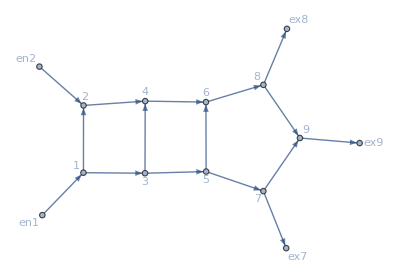

```mathematica
d2e1["FG"]
```

#### Non-linear case

```mathematica
alpha = .99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,2.4},GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,PlotRange->{1-0.1,4.7},GridLines->Automatic]&/@MFGEquations["BEL"]
```